# 2020 回顾

#### by GWDx

-Graphics-

{i for i in things(2020)}

## Course

### 大一上

#### 1-4 ~ 1-12 test

### 大一下

#### 4-25 物理作业

```mathematica
FullSimplify@Integrate[(μ R^2 Cos[t]^2)/(2(R^2 Cos[t]^2+(z-R Sin[t])^2)^(3/2)) (q ω Cos@t)/(4π),{t,-π/2,π/2},Assumptions->{z≠0,z≠R,z≠-R,R≠0}]
```

-(q (R^2 (√((R-z)^2)-√((R+z)^2))+z^2 (√((R-z)^2)-√((R+z)^2))+R z (√((R-z)^2)+√((R+z)^2))) μ ω)/(12 π R z^3)

#### 6-7 转专业申请 6-13 & 6-14 实验报告 8-23 ~ 9-11 考试复习

### 大二上

#### 9-28 做到 23:00 的大物实验 10 爱玩 MC 的 复变老师 12-25 Brainfuck-Verilog

## Computer

## Software (extraordinary)

### Program Language

3 ★		Mathematica
9		iverilog
11-4 ★	Python
11-10	mingw64 (C++)
12		Java
12		nodejs

### Editor

9		Notepad++
11-10 ★	VS Code

### Other

8		VirtualBox

## Git

### 11-10 join GitHub and create Euler-Project 12-17 fork goreviewpartner and add kata_analysis

## Bat

### 11-10 togit.bat

for /l %%i in (%1,1,%2) do (git add %%i.wl)
git status & pause
git commit -m “add %1-%2”
git push & pause

### 11-19 Compile+.bat

@for /r %%i in (*.v) do iverilog -o temp.txt %%i || pause
del temp.txt
pause

## Python

### 11-5 ~ 11-6 Hackergame 2020

#### 8.nb

(lambda x:print((x+str((x,)))[::-1],end=""))('(lambda x:print((x+str((x,)))[::-1],end=""))',)

),'))""=dne,]1-::[))),x((rts+x((tnirp:x adbmal('())""=dne,]1-::[))),x((rts+x((tnirp:x adbmal(

参考：	https://www.zhihu.com/question/37046157/answer/123735086

### 12-31 brainfuck.nb

```mathematica
brainfuck[s_]:={StringLength@s,ExternalEvaluate[py,"brainfuck(\""<>s<>"\",\"\")"]}
brainfuck@"->+>>+++[+++++[>++++[>++++<-]<-]<+]>>>++.+++.>+.>--."
```

{52,rua~}

## Mathematica

### 1-23 image3.nb

```mathematica
Show[j=ImageAssemble@Apply[ColorCombine[{#1⟦1⟧,#2⟦2⟧,#3⟦3⟧},"RGB"]&,Map[f,Round[9Rescale@Apply[{#1,#2,#3}&,ImageData@i,{2}]],{3}],{2}],ImageSize->400]
```

-Graphics-

参考：	https://www.bilibili.com/video/BV1pW411M7ru

### 2-29 mine11.nb

```mathematica
Grid[MapAt[Highlighted[#,FrameMargins->0]&,Array[f,{m,n}],Join[xx,yy,zz]],ItemSize->All]
```

■ | 2 | 2 | ■ | 2 | ■ | ■ | 2 | ■ | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 2 |      |      |      |      |      |     
2 | ■ | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 1 | 1 | 2 | 2 | 1 | 0 | 2 | ■ | 2 | 0 | 0 | 0 | 1 | ■ | 4 |      |      |      |      |      |     
1 | 1 | 1 | 1 | ■ | 2 | 2 | ■ | 2 | 1 | 1 | ■ | ■ | 3 | 1 | 4 | ■ | 4 | 1 | 1 | 0 | 1 | 2 | ■ |      |      |      |      |      |     
0 | 0 | 0 | 1 | 2 | ■ | 2 | 2 | ■ | 1 | 1 | 3 | ■ | 3 | ■ | 4 | ■ | 4 | ■ | 1 | 0 | 0 | 1 | 2 |      |      |      |      |      |     
2 | 2 | 2 | 1 | 2 | 2 | 3 | 4 | 3 | 2 | 0 | 1 | 1 | 2 | 1 | 3 | ■ | 5 | 3 | 2 | 0 | 0 | 0 | 1 |      |      |      |      |      |     
■ | ■ | 3 | ■ | 1 | 1 | ■ | ■ | ■ | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 3 | ■ | ■ | 1 | 1 | 2 | 2 | 2 |      |      |      |      |      |     
3 | ■ | 3 | 1 | 1 | 1 | 4 | ■ | 6 | 3 | 3 | ■ | 3 | 1 | 0 | 0 | 2 | ■ | 3 | 1 | 1 | ■ | ■ | 2 |      |      |      |      |      |     
1 | 1 | 1 | 0 | 1 | 1 | 3 | ■ | ■ | ■ | 3 | ■ | ■ | 2 | 1 | 0 | 2 | 2 | 2 | 1 | 2 | 3 | 3 |      |      |      |      |      |      |     
0 | 1 | 2 | 3 | 3 | ■ | 3 | 3 | 4 | 2 | 2 | 2 | 3 | ■ | 1 | 0 | 1 | ■ | 2 | 3 | ■ | 2 | 1 |      |      |      |      |      |      |     
0 | 1 | ■ | ■ | ■ | 2 | 2 | ■ | 2 | 1 | 0 | 0 | 1 | 1 | 2 | 1 | 2 | 2 |      |      | ■ | 3 | 2 |      |      |      |      |      |      |     
0 | 1 | 3 | 4 | 3 | 2 | 2 | 3 | ■ | 2 | 1 | 0 | 1 | 1 | 3 | ■ | 3 | 2 |      |      |      |      |      |      |      |      |      |      |      |     
0 | 0 | 2 | ■ | 2 | 1 | ■ | 2 | 2 | ■ | 1 | 1 | 2 | ■ | 3 | ■ | 3 | ■ | 2 |      |      |      |      |      |      |      |      |      |      |     
1 | 1 | 4 | ■ | 3 | 1 | 1 | 1 | 1 | 2 | 3 | 4 | ■ | 3 | 2 | 1 | 3 | 3 |      |      |      |      |      |      |      |      |      |      |      |     
2 | ■ | 3 | ■ | 2 | 0 | 0 | 0 | 0 | 1 | ■ | ■ | ■ | 4 | 1 | 1 | 2 | ■ |      |      | 3 |      |      |      |      |      |      |      |      |     
■ | 3 | 2 | 1 | 1 | 0 | 0 | 0 | 0 | 2 | 4 |      | ■ | 3 | ■ | 1 | 2 | ■ | 3 | 2 |      |      |      |      |      |      |      |      |      |     
■ | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | ■ |      | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 |      |      |      |      |      |      |      |      |      |

### 4-5 icon+.nb

```mathematica
Graphics3D[{EdgeForm@{Thickness[.0015],Opacity[0]},
GraphicsComplex[vv,{FaceForm[Opacity[.7],Opacity[.1]],Polygon@PolyhedronData["Icosahedron","FaceIndices"]},VertexColors->Array[g,12]],
GraphicsComplex[vv,{EdgeForm[],Opacity[.7],Polygon@{{1,3,2,4},{5,6,8,7},{9,10,12,11}}},VertexColors->Array[h,12]]},Boxed->False,ViewVector->{{7,7,7},{0,0,0}},ViewAngle->Pi/16]
```

-Graphics3D-

### 4-8 pendulum.nb

```mathematica
<<(NotebookDirectory[]<>"mxs\\pendulum.mx")
Animate[ken[t],{t,0,24.389},AnimationRunning->False,AnimationRate->0.3]
```

### 5-10 collision.nb

```mathematica
<<(NotebookDirectory[]<>"mxs\\collision.mx")
Manipulate[{Show[Plot[eedge[x],{x,-10,10},AspectRatio->1],Graphics[Circle/@p[t]],PlotRange->{{-15,12},{-10,12}},ImageSize->250],Grid@Map[NumberForm[#,{3,2},NumberSigns->{"-", " "}]&,p'[t],{2}]},{t,0,10}]
```

### 12-16 Physical-Experiment

```mathematica
plot[mod/.fit,{mark,{60,Above}},{16,88},{{10,95},{.22,.285}},{gridT,gridR},{"T/°C","R_Cu/Ω"},{ticksT,ticksR},da]
```

-Graphics-

```mathematica
format@export[Subscript[r, α][0],√((Subscript[u, b]/b)^2+(Subscript[u, k]/k)^2-2 Subscript[ρ, b,k](Subscript[u, b]/b)(Subscript[u, k]/k)),holdRule@{Subscript[u, b],Subscript[u, k],Subscript[ρ, b,k]}]
```

r_α[0]=√((u_b/b)^2+(u_k/k)^2-(2 ρ_(b,k) u_b u_k)/(b k))=√(((5.516×10^-4)/b)^2+((1.336×10^-5)/k)^2-(2 -0.9084 (5.516×10^-4) (1.336×10^-5))/(b k))=0.01828

## Hobby

## Go

#### 5-19 restart

GPU
	受伤
 ★	柯洁炸鱼

#### 7-31 野狐 1 d 8 高中同学

## MC

## Run

#### 4-4 restart

#### 11-6 1500m 5’12’’

## Bilibili

```mathematica
BilibiliAns=TakeDrop[Prepend[Take[BilibiliData,All,4],Style[#,20]&/@{"","关注时间","icon","ID"}],8];
Row[Grid[#,Alignment->{Left,Center},Frame->All,FrameStyle->LightGray,ItemSize->{Automatic,All}]&
/@BilibiliAns,"\t\t"]
```

| 关注时间 | icon | ID
1 | 2019-09-27(Fri) 13:04 | -Graphics- | 薛定饿了么
2 | 2019-12-01(Sun) 10:54 | -Graphics- | 代表校长开除你
3 | 2020-01-20(Mon) 13:46 | -Graphics- | 五十铃怜
4 | 2020-02-23(Sun) 19:02 | -Graphics- | 二階堂真紅天下第一
5 | 2020-03-06(Fri) 18:25 | -Graphics- | 小台乐
6 | 2020-03-17(Tue) 00:32 | -Graphics- | 子乾爱科学
7 | 2020-03-25(Wed) 22:51 | -Graphics- | 罗翔说刑法8 | 2020-03-29(Sun) 00:08 | -Graphics- | 田老师围棋
9 | 2020-04-26(Sun) 14:40 | -Graphics- | 笔记本维修厮
10 | 2020-04-29(Wed) 23:02 | -Graphics- | 舞秋风台
11 | 2020-05-07(Thu) 16:56 | -Graphics- | 3Blue1Brown
12 | 2020-06-10(Wed) 13:02 | -Graphics- | 胡翼飞
13 | 2020-07-26(Sun) 19:14 | -Graphics- | 柯洁
14 | 2020-10-10(Sat) 23:01 | -Graphics- | 老狼zhihu
15 | 2020-12-20(Sun) 17:17 | -Graphics- | 如花似玉

## Zhihu

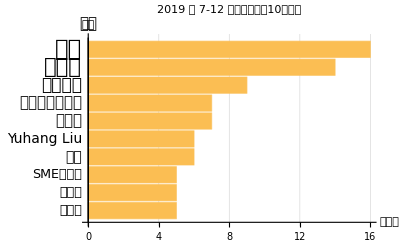
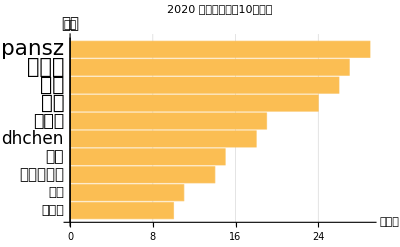

```mathematica
Row[barChart@@@({{voteYearData[2019], 5, "2019 年 7-12 月赞同最多的10个用户", 2}, {voteYearData[2020], 10, "2020 年赞同最多的10个用户", 1}})/.highlightRule,"\t"]
```

## Time

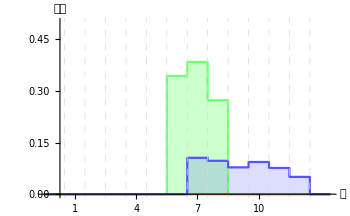
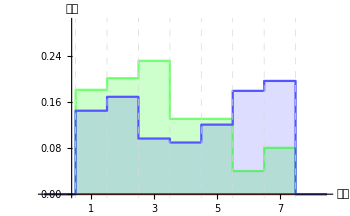
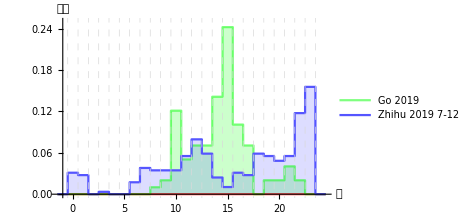
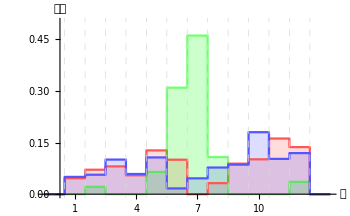
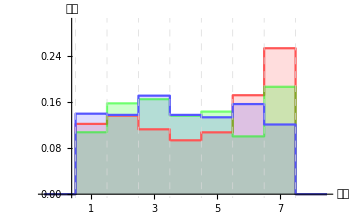
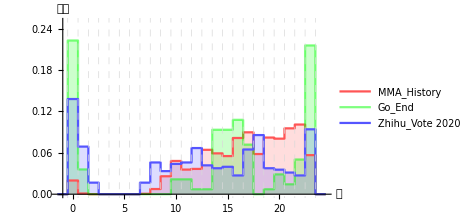
2019 年围棋结束时间、知乎赞同时间的分布情况 |  | 
-Graphics- | -Graphics- | -Graphics-

2020 年 MMA笔记本修改时间、围棋结束时间、知乎赞同时间的分布情况 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
range=#1->PlotRange->{0,#2}&@@@({{1, .5}, {2, .3}, {3, .25}});
ansPlot[{data_,legends_},rules___]:=timeListStepPlot[data,"Probability"->True,PlotStyle->color,ImageSize->350,"RulesAt"->{range,3->PlotLegends->legends},rules]
Grid[{{Style["2019 年围棋结束时间、知乎赞同时间的分布情况",15],SpanFromLeft,SpanFromLeft},
ansPlot[Transpose@({{{}, None}, {goTimeData2019, "Go 2019"}, {voteYearTime[2019], "Zhihu 2019 7-12"}}),"ScalingAt"->{{3,1}->.5}],
{Style["\n2020 年 MMA笔记本修改时间、围棋结束时间、知乎赞同时间的分布情况",15],SpanFromLeft,SpanFromLeft},
ansPlot[Transpose@({{Join@@nbData, "MMA_History"}, {goTimeData2020, "Go_End"}, {voteYearTime[2020], "Zhihu_Vote 2020"}})]},Alignment->{{Center,Left,Center,Left},Automatic}]
```

由于2019年我对Mathematica中的规则以及函数式编程几乎没有了解，故不将其计入；
	而2019年上半年知乎的赞同情况也没有参考价值。

## Thanks

```mathematica
itemShow[i_Image]:=Show[i,ImageSize->100];
itemShow[i_Graphics]:=Show[i,ImageSize->100];
itemShow[s_String]:=Style[s,30,Gray];
itemShow[t_]:=t
thanks=({{-Graphics-, -Graphics-, -Graphics-, "…"}, {-Graphics-, -Graphics-, -Graphics-, SpanFromAbove}, {-Graphics-, -Graphics-, -Graphics-, SpanFromAbove}});
thanksItem=Map[itemShow,thanks,{2}];
Grid[thanksItem,Alignment->{Center,Center},Frame->{None,None,{{1,1}->True,({{1, 2}, {2, 3}})->True,({{1, 3}, {1, 3}})->False}},FrameStyle->LightGray,Spacings->{1,1}]
```

-Graphics- | -Graphics- | -Graphics- | …
-Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- |

## Ending

#### Bilibili: https://space.bilibili.com/442365922 @甘文迪许

#### GitHub: https://github.com/GWDx @GWDx